# CovidNet 4.0 Future Forecasting of COVID-19 Copyrights (c) Essam Rashed (essam.rashed@nitech.ac.jp), NITech, Nagoya, JP Updated: 13 Jan. 2022

[1] Google Mobility (retail)
[2] Google Mobility (Grocery)
[3] Google Mobility (Parks)
[4] Google Mobility (Transit)
[5] Google Mobility (Work)
[6] Google Mobility (Residential)
[7] Mobility (Downtown Area)
[8] Maximum Temperature
[9] Minimum Temperature
[10] Average Humidity
[11] Week day label
[12] State of emergency label
[13] Variant infectivity
[14] Twitter (drinking)
[15] Twitter (Karaoke)
[16] Twitter (BBQ)
[17] Daily Positive Cases
[18] Serious Cases
[19] Hospitalized Cases
[20] Death Cases
[21] Discharges Cases
[22] vaccination efficiency model

```mathematica
MOSTUPDATED=720;(*720 -> 13 Jan 2022 *)
```

```mathematica
XP="future";
```

```mathematica
City="Tokyo";
```

```mathematica
SelectedInputs={4,13,14,22};
```

```mathematica
SelectedOutput=17; (*17P - 18S - 19H *)
```

```mathematica
EXPNUM="20220114_P_4_13_14_22";
```

```mathematica
NotebookEvaluate["/home/essam/COVID_"<>XP<>"/Notebooks/Train.nb"];
```

Architecture: ArchOrig

City: Tokyo & Data: {4,13,14,22}->17

Training: {2020,4,1}->{2022,1,11}

Val: [0., 5773.] and Scale: [0.2, 0.8]

Variant weights: {2.4,1.6,1.1,1.2,1.,1.,1.}

Days are: 14 and 14

Epochs: 500 & BS: 32

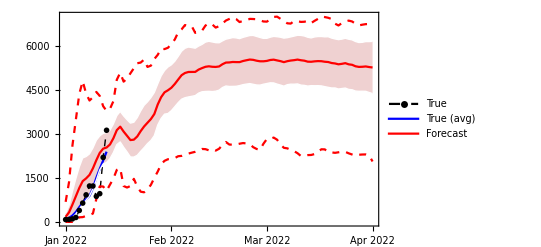

```mathematica
t=DateListPlot[{rv,rvavg,p,max,min,min95,max95},,PlotMarkers->{{"OpenMarkers",Small},None,None,None,None,None,None},PlotStyle->{{Black,Thin,Dashed},{Blue},{Red},{Dashed,Red},{Dashed,Red},{Thin,White},{Thin,White}},Filling->{7->{{6},{RGBColor[.7,.1,.1,.2]}}},DateTicksFormat->{"MonthShort", "/", "Day"},PlotLegends->Placed[{"True","True (avg)","Forecast"},{.9,.1}], ImageSize->Full]
```

```mathematica
(*Clear[net];Clear[trained];*)
```

```mathematica
(*Clear[TrainingDataSingle]; Clear[TestingData];Clear[TrainingData];*)
```

```mathematica
(*Clear[InputTrain];Clear[OutputTrain];Clear[InputTest];Clear[all];Clear[alltmp];*)
```